Type II & Type III Oscillations

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Place relevant file string for Dynamica here *)
Quiet[<<".../Dynamica.m"]
```

Dynamica (Version 1.0.11 - 5/8/2021), Copyright(c) 1993-2021 Randall D. Beer. All rights reserved.

THIS SOFTWARE IS DISTRIBUTED 'AS IS'. NO WARRANTY OF ANY KIND IS EXPRESSED OR IMPLIED.

## SYSTEMS

## SI

### F2G, A4A, A4C

```mathematica
Clear[f,ds,u,v,theta,beta,k1]
```

```mathematica
SI = DynamicalSystem[{
f*(S+theta*F)*(1-(S + F)/k1)- ds*S - beta*S*F,
beta * S*F -(ds + v)* F
},
{{S,-10,200},{F,-10,200}},
{{f,0,1},{ds,0.001,0.14},{beta,0,2},{v,0,0.2},{theta,0,1}, {k1,0.01,10}}]
```

DynamicalSystem[«2 ODEs»,{S,F},{f,ds,beta,v,theta,k1}]

```mathematica
SI = SI/.{f->0.1, beta->0.055, v->0.05157, theta->0.05, k1->30}
```

DynamicalSystem[«2 ODEs»,{S,F},{ds},{beta→0.055,f→0.1,k1→30,theta→0.05,v→0.05157}]

Warning: A convergence failure occurred during continuation

Warning: A convergence failure occurred during continuation

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,k1,ds}={0.0150740924912979,0,0.01,-0.0507409249129786}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,k1,ds}={0.955818181818182,0,0.965472910927456,0.001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,k1,ds}={2.33184615384615,0,10,0.0766815384615385}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,k1,ds}={0,0,10,0.1}

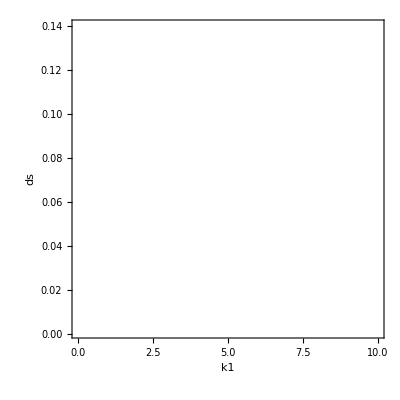

```mathematica
PCSI = DisplayParameterChart[SI,{k1,ds},MaxSteps->Infinity, MaxStepSize->0.1]
```

#### R0 & Sin

```mathematica
Clear[f,ds,v,beta,theta,k1]
```

```mathematica
dSSI=f*(S+theta*F)*(1-(S + F)/k1)- ds*S - beta*S*F;
dFSI=beta*S*F -(ds + v)* F;
```

```mathematica
solsSI=Solve[{dSSI==0,dFSI==0},{S,F}];
```

```mathematica
solsSI[[3]]
```

{S→(ds+v)/beta,F→1/(2 beta^2 f theta)(-beta ds f-beta^2 ds k1-beta ds f theta+beta^2 f k1 theta-beta f v-beta^2 k1 v-beta f theta v-√((beta ds f+beta^2 ds k1+beta ds f theta-beta^2 f k1 theta+beta f v+beta^2 k1 v+beta f theta v)^2-4 beta^2 f theta (ds^2 f+beta ds^2 k1-beta ds f k1+2 ds f v+beta ds k1 v-beta f k1 v+f v^2)))}

```mathematica
f = 0.1;
beta= 0.055;
v = 0.05157;
```

```mathematica
solsSI[[2]]/.{ds->0.06,k1->30}
```

{S→12.,F→0}

Get Boundary S & A to plug into R0

```mathematica
SatBSI=solsSI[[2,1,2]];
```

R0 Equation

```mathematica
R0SI= (beta*SatBSI)/(ds+v) ;
```

```mathematica
S0SI = f/ds;
```

#### Construct Chart

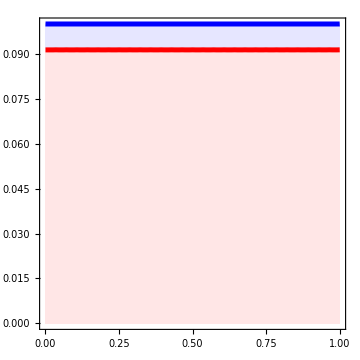

```mathematica
Clear[theta];
k1 = 30;
FCSI1= Show[
RegionPlot[S0SI>=1 ,{theta,0,1},{ds,0,0.14}, BoundaryStyle->None,PlotStyle->Lighter[Blue,0.9]],
RegionPlot[R0SI>=1 ,{theta,0,1},{ds,0,0.14}, BoundaryStyle->None,PlotStyle->Lighter[Red,0.9]],
ContourPlot[S0SI==1,{theta,0,1},{ds,0.00001,0.14},ContourStyle->{Blue,Thickness->0.01}],
ContourPlot[R0SI==1,{theta,0,1},{ds,0.00001,0.14},ContourStyle->{Red,Thickness->0.01}],
ImageSize->Medium,
LabelStyle->{16,Black},AxesOrigin->{0,0},
AspectRatio->1,PlotRange->All, PlotRangeClipping->False
]
```

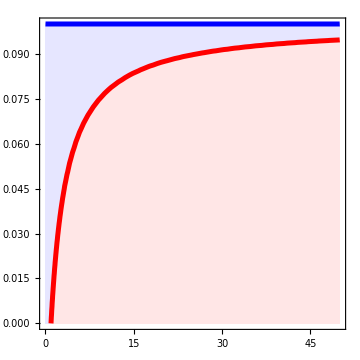

```mathematica
Clear[k1];
theta = 0.05;
FCSI2= Show[
RegionPlot[S0SI>=1 ,{k1,0,50},{ds,0,0.14}, BoundaryStyle->None,PlotStyle->Lighter[Blue,0.9]],
RegionPlot[R0SI>=1 ,{k1,0,50},{ds,0,0.14}, BoundaryStyle->None,PlotStyle->Lighter[Red,0.9]],
ContourPlot[S0SI==1,{k1,0,50},{ds,0.00001,0.14},ContourStyle->{Blue,Thickness->0.01}],
ContourPlot[R0SI==1,{k1,0,50},{ds,0.00001,0.14},ContourStyle->{Red,Thickness->0.01}],
ImageSize->Medium,
LabelStyle->{16,Black},AxesOrigin->{0,0},
AspectRatio->1,PlotRange->All, PlotRangeClipping->False
]
```

### A4E

```mathematica
solsSI[[4]]/.{ds->0.01,theta->0.1}
```

{S→1.11945,F→33057.9 (-0.000355567+√(-0.0000605 (0.000379086-0.000304772 k1)+(0.000355567+0.000171124 k1)^2)-0.000171124 k1)}

```mathematica
solsSI[[4]]/.{ds->0.06,theta->0.1}
```

{S→2.02855,F→33057.9 (-0.000644317+√(-0.0000605 (0.00124479-0.000245454 k1)+(0.000644317+0.000322374 k1)^2)-0.000322374 k1)}

```mathematica
SstarSI= solsSI[[4]][[1]][[2]];
FstarSI= solsSI[[4]][[2]][[2]];
```

```mathematica
Solve[R0SI==1,ds]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{ds→(0.00001 (-5157.+10000. k1))/(1.+k1)}}

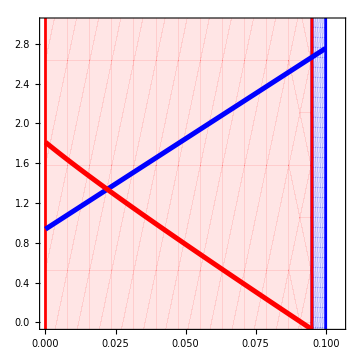

```mathematica
k1=30;
theta = 0.05;
P2SI= Show[
RegionPlot[0.1 > x>0.0951,{x,0,0.15},{y,-10,10}, BoundaryStyle->Blue,PlotStyle->{Blue, Opacity[0.1]},PlotPoints->200],
RegionPlot[0.0951> x>-1,{x,0,0.15},{y,-10,10}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],

Plot[Re[SstarSI] ,{ds,0,0.1}, PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Re[FstarSI],{ds,0,0.0951}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{{0,0.105},{-0.01,3}},
Frame->True,AxesOrigin->{0,0.00},
 LabelStyle->{Black,16},ImageSize->Medium
]
```

### A4G

```mathematica
Clear[f,ds,v,beta,theta,k1]
```

```mathematica
FullSimplify[D[dSSI,S]]
```

-ds-beta F-(f (F-k1+2 S+F theta))/k1

```mathematica
JSSSI = -ds-beta FstarSI-(f (FstarSI-k1+2 SstarSI+FstarSI theta))/k1;
```

```mathematica
FullSimplify[D[dSSI/S,S]]
```

-(f (S^2+F (-F+k1) theta))/(k1 S^2)

```mathematica
DDS = -(f (SstarSI^2+FstarSI (-FstarSI+k1) theta))/(k1 SstarSI^2);
```

```mathematica
f = 0.0153;
v = 0.05157;
theta = 0.05;
k1 = 30;
beta= 0.055;
```

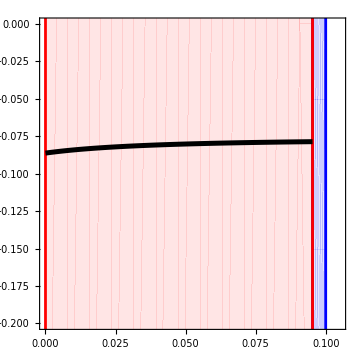

```mathematica
Show[
RegionPlot[0.1 > x>0.0953,{x,0,0.15},{y,-10,10}, BoundaryStyle->Blue,PlotStyle->{Blue, Opacity[0.1]},PlotPoints->200],
RegionPlot[0.0953> x>-1,{x,0,0.15},{y,-10,10}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],

Plot[Re[JSSSI],{ds,0,0.0953}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{{0,0.105},{-0.2,0}},
Frame->True, LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

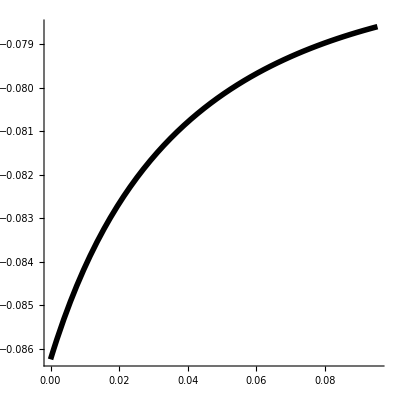

```mathematica
Plot[Re[JSSSI],{ds,0,0.0953}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16]
```

## SIZ

### F2H, A4B, A4D

```mathematica
Clear[e,h,f,ds,dz,beta,v,o,theta,r,k1]
```

```mathematica
SIZ = DynamicalSystem[{
f*(S+theta*F)*(1-(S + F)/k1)- ds*S - u*f*S*Z,
beta*f*S*Z -(ds + v)* F,
o(ds + v)*F - dz Z
},
{{S,-10,200},{F,-10,200},{Z,-10,200}},
{{e,0,100},{h,0,1},{f,0,1},{dz,0.001,1},{ds,0.001,0.14},{o,0.001,1000},{beta,0,2},{v,0,0.2},{theta,0,1}, {k1,0.01,50}}]
```

DynamicalSystem[«3 ODEs»,{S,F,Z},{e,h,f,dz,ds,o,u,v,theta,k1}]

```mathematica
SIZ = SIZ/.{e->8,h -> 0.2314, f->0.1, beta->0.055, v->0.05157, k1->30,theta->0.05,o ->483.8,dz->0.9}
```

DynamicalSystem[«3 ODEs»,{S,F,Z},{ds},{dz→0.9,e→8,f→0.1,h→0.2314,k1→30,o→483.8,theta→0.05,u→0.055,v→0.05157}]

Warning: A convergence failure occurred during continuation

Warning: A convergence failure occurred during continuation

Warning: A convergence failure occurred during continuation

«3 more identical outputs»

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,Z,theta,ds}={0.338231425457552,0,0,0,0.0988725619151415}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,Z,theta,ds}={0,0,0,1,0.1}

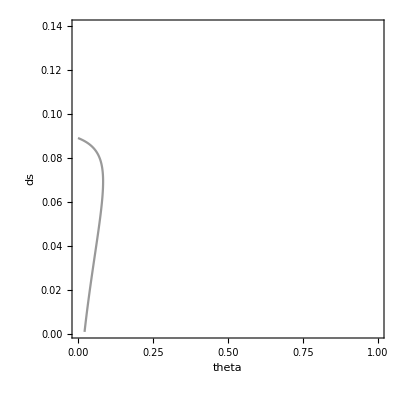

```mathematica
PCSIZ1 = DisplayParameterChart[SIZ,{theta,ds},MaxSteps->Infinity]
```

Warning: A convergence failure occurred during continuation

Warning: A convergence failure occurred during continuation

Warning: A convergence failure occurred during continuation

«1 more identical outputs»

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,Z,k1,ds}={0.338231425457529,0,0,0.341647904502531,0.001}

Only codimension 1 solutions can be followed

Found a codimension 2 solution at {S,F,Z,k1,ds}={0,0,0,0.01,0.1}

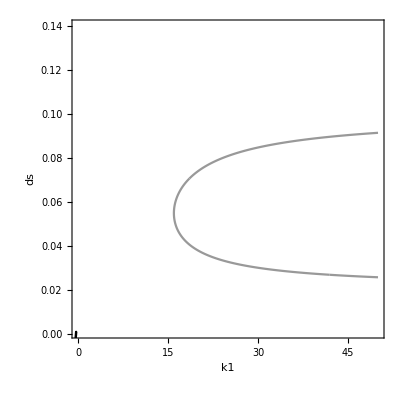

```mathematica
PCSIZ2 = DisplayParameterChart[SIZ,{k1,ds},MaxSteps->Infinity]
```

#### R0 & Sin

```mathematica
Clear[f,ds,dz,beta,v,o,theta,r,k1]
```

```mathematica
dSSIZ=f*(S+theta*F)*(1-(S + F)/k1)- ds*S - beta*f*S*Z;
dFSIZ=beta*f*S*Z -(ds + v)* F;
dZSIZ = o(ds + v)*F - dz Z;
```

```mathematica
solsSIZ=Solve[{dSSIZ==0,dFSIZ==0,dZSIZ==0},{S,F,Z}];
```

```mathematica
solsSIZ[[2]]/.{k1->30,ds->0.05,f->0.1}
```

{S→15.,F→0,Z→0}

Get Boundary S & A to plug into R0

```mathematica
SatBSIZ=solsSIZ[[2,1,2]];
```

R0 Equation

```mathematica
R0SIZ= (beta*f*SatBSIZ)/(ds+v) (o(ds+v))/dz;
```

```mathematica
S0SIZ = f/ds;
```

#### Construct Chart

```mathematica
Clear[k1,ds]
f = 0.1;
dz = 0.9;
beta = 0.055;
v = 0.05157;
o = 483.8;
theta = 0.05;
k1 = 30;
```

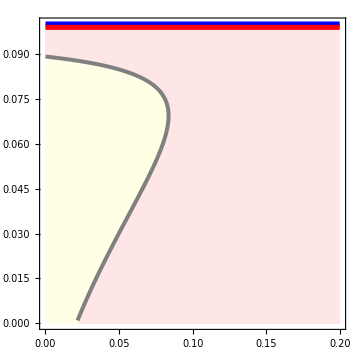

```mathematica
FCSIZ= Show[
RegionPlot[S0SIZ>=1 ,{theta,0,0.2},{ds,0,0.14}, BoundaryStyle->None,PlotStyle->Lighter[Blue,0.9], PlotPoints->100],
RegionPlot[R0SIZ>=1 ,{theta,0,0.2},{ds,0,0.14}, BoundaryStyle->None,PlotStyle->Lighter[Red,0.9]],
ListLinePlot[PCSIZ1[[1]][[1]][[1]][[3]][[1]],PlotStyle->{Gray,Thickness->0.008},Filling->Bottom,FillingStyle->Lighter[Yellow,0.9]],
ContourPlot[S0SIZ==1,{theta,0,0.2},{ds,0.00001,0.14},ContourStyle->{Blue,Thickness->0.01}],
ContourPlot[R0SIZ==1,{theta,0,0.2},{ds,0.00001,0.14},ContourStyle->{Red,Thickness->0.01}],(* Same here as S0 *)
ImageSize->Medium,
LabelStyle->{16,Black},AxesOrigin->{0,0},
AspectRatio->1,PlotRange->All, PlotRangeClipping->False
]
```

```mathematica
PCSIZ2[[1]][[1]][[2]][[3]][[1]]
```

{{50,0.091499876284524},{49.9962489917502,0.0914991805063437},18030,{50,0.0258268779429893},{50,0.0258268779429893}}
 |  |  |  |

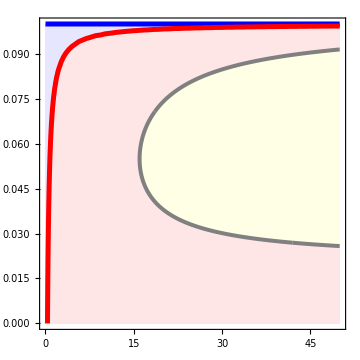

```mathematica
FCSIZ2= Show[
RegionPlot[S0SIZ>=1 ,{k1,0,50},{ds,0,0.14}, BoundaryStyle->None,PlotStyle->Lighter[Blue,0.9], PlotPoints->100],
RegionPlot[R0SIZ>=1 ,{k1,0,50},{ds,0,0.14}, BoundaryStyle->None,PlotStyle->Lighter[Red,0.9]],
ListLinePlot[PCSIZ2[[1]][[1]][[2]][[3]][[1]],PlotStyle->{Gray,Thickness->0.008},Filling->Bottom,FillingStyle->Lighter[Yellow,0.9]],
ContourPlot[S0SIZ==1,{k1,0,50},{ds,0.00001,0.14},ContourStyle->{Blue,Thickness->0.01}],
ContourPlot[R0SIZ==1,{k1,0,50},{ds,0.00001,0.14},ContourStyle->{Red,Thickness->0.01}],(* Same here as S0 *)
ImageSize->Medium,
LabelStyle->{16,Black},AxesOrigin->{0,0},
AspectRatio->1,PlotRange->All, PlotRangeClipping->False
]
```

#### Time Series

```mathematica
Clear[k1,ds]
f = 0.1;
dz = 0.9;
beta = 0.055;
v = 0.05157;
o = 483.8;
theta = 0.05;
```

```mathematica
Clear[ds,k1]
ds = 0.06;
ParaSIZ=ParametricNDSolveValue[
{S'[t]== f*(S[t]+theta*F[t])*(1-(S[t] + F[t])/k1)- ds*S[t] - beta*f*S[t]*Z[t],
F'[t] == beta*f*S[t]*Z[t] -(ds + v)* F[t],
Z'[t] == o(ds + v)*F[t] - dz Z[t],
S[0]==101,F[0]==201, Z[0]==100},{S,F,Z},{t,0,6000},{k1}];
```

```mathematica
Manipulate[
Show[LogPlot[Evaluate[#[t]& /@ParaSIZ[k1]],{t,0,5500},PlotRange->{{3000,3500},{0.005,100}},
 PlotStyle->{{Blue,Thick},{Red,Thick},{Gray,Thick}},
PlotLegends->{"Susceptible","Infected","Propagules"},TicksStyle->10,AspectRatio->1, LabelStyle->16, Frame->True, FrameLabel->{"Time","Log Concentration"}, FrameStyle->Black]],
{{k1,30},1,100}]
```

### A4F, A5A

```mathematica
ZstarSIZ=solsSIZ[[4]][[3]][[2]];
SstarSIZ = solsSIZ[[4]][[1]][[2]];
FstarSIZ= solsSIZ[[4]][[2]][[2]];
```

```mathematica
Clear[k1,ds]
f = 0.1;
dz = 0.9;
beta = 0.055;
v = 0.05157;
o = 483.8;
theta = 0.05;
k1 = 30;
```

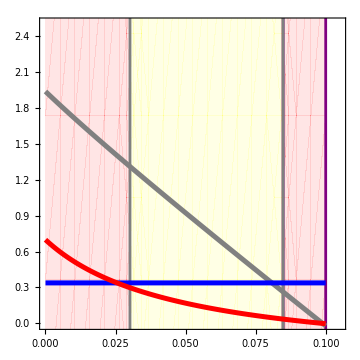

```mathematica
Show[
RegionPlot[0.03015> x>-1,{x,0,0.1},{y,-1,25}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[1> x>0.0848,{x,0,0.1},{y,-1,25}, BoundaryStyle->Purple,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0848> x>0.03015,{x,0,0.1},{y,-1,25}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[ZstarSIZ]*0.1,{ds,0,0.1}, PlotStyle->{Gray,Thickness[0.01]},AspectRatio->1,LabelStyle->16,PlotPoints->100],

Plot[Re[SstarSIZ],{ds,0,0.1}, PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

Plot[Re[FstarSIZ],{ds,0,0.1}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16, PlotPoints->200],

PlotRange->{{0,0.105},{0,2.5}},
Frame->True,
 LabelStyle->{Black,16},ImageSize->Medium
]
```

### F2I, A4H

```mathematica
Clear[f,dz,u,v,o,theta,r,ds,k1]
```

```mathematica
(*JSS*)
FullSimplify[D[dSSIZ/S,S]]
```

-(f (S^2+F (-F+k1) theta))/(k1 S^2)

```mathematica
JSSSIZ = -ds-(f (FstarSIZ-k1+2 SstarSIZ+FstarSIZ theta))/k1-f beta ZstarSIZ;
SelfLimSIZ= -ds-(f (FstarSIZ-k1+2 SstarSIZ+FstarSIZ theta))/k1;
ClearanceSIZ= -f beta ZstarSIZ;
```

```mathematica
f = 0.1;
dz = 0.9;
beta = 0.055;
v = 0.05157;
o = 483.8;
theta = 0.05;
k1 = 30;
```

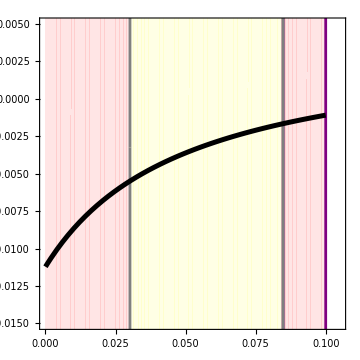

```mathematica
P4SIZ = Show[
RegionPlot[0.03015> x>-1,{x,0,0.1},{y,-1,25}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[1> x>0.0848,{x,0,0.1},{y,-1,25}, BoundaryStyle->Purple,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0848> x>0.03015,{x,0,0.1},{y,-1,25}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Re[JSSSIZ],{ds,0,0.1}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{{0,0.105},{-0.015,0.005}},
Frame->True, LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

### A5

#### A5B

```mathematica
Clear[f,ds,dz,beta,v,o,theta,r,k1]
```

```mathematica
J11SIZ = FullSimplify[D[dSSIZ,S]]
```

```mathematica
Sstar = solsSIZ[[4]][[1]][[2]];
Istar = solsSIZ[[4]][[2]][[2]];
Zstar = solsSIZ[[4]][[3]][[2]];
direct = FullSimplify[D[J11SIZ,ds]];
indirectI = D[J11SIZ,F] *D[Istar,ds];
indirectZ = D[J11SIZ,Z]* D[Zstar,ds];
indirectTotal = indirectI + indirectZ;
```

```mathematica
f = 0.1;
dz = 0.9;
beta = 0.055;
v = 0.05157;
o = 483.8;
theta = 0.05;
k1 = 30;
```

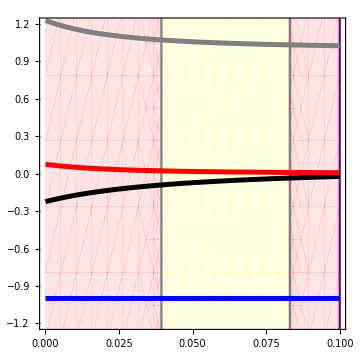

```mathematica
Show[
RegionPlot[0.0394> x>-1,{x,0,0.1},{y,-5,5}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[1> x>0.0831,{x,0,0.1},{y,-5,5}, BoundaryStyle->Purple,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0831> x>0.0394,{x,0,0.1},{y,-5,5}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[(J11SIZ/.{S->Sstar,F->Istar,Z->Zstar})*20,{ds,0,0.1}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[direct,{ds,0,0.1}, PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[indirectI,{ds,0,0.1}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[indirectZ,{ds,0,0.1}, PlotStyle->{Gray,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{All,{-1.2,1.2}},
Frame->True,
(*FrameTicks->{{{-0.005,0.00,0.005,0.01,0.015},None},{{0,0.05,0.1},None}}, *)LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

#### A5C

```mathematica
Clear[f,ds,dz,beta,v,o,theta,r,k1]
```

```mathematica
J11SIZ = FullSimplify[D[dSSIZ,S]]
```

```mathematica
Sstar = solsSIZ[[4]][[1]][[2]];
Istar = solsSIZ[[4]][[2]][[2]];
Zstar = solsSIZ[[4]][[3]][[2]];
direct = FullSimplify[D[J11SIZ,k1]];
indirectI = D[J11SIZ,F] *D[Istar,k1];
indirectZ = D[J11SIZ,Z]* D[Zstar,k1];
indirectTotal = indirectI + indirectZ;
```

```mathematica
f = 0.1;
dz = 0.9;
beta = 0.055;
v = 0.05157;
o = 483.8;
theta = 0.05;
ds = 0.05;
```

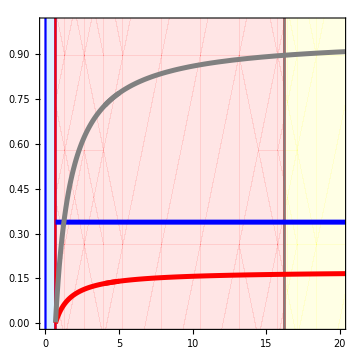

```mathematica
Show[
RegionPlot[0.676> x>-1,{x,0,50},{y,-1,11}, BoundaryStyle->Blue,PlotStyle->{LightBlue}],
RegionPlot[16.242> x>0.676,{x,0,50},{y,-1,11}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[x>16.242,{x,0,50},{y,-1,11}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[Sstar,{k1,0.68,50}, PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Istar,{k1,0.68,5}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Istar,{k1,0.68,50}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Zstar*0.1,{k1,0.68,5}, PlotStyle->{Gray,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Zstar*0.1,{k1,0.68,50}, PlotStyle->{Gray,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{{0,20},{0,1}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

#### A5D

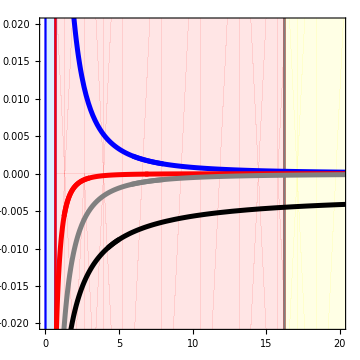

```mathematica
Show[
RegionPlot[0.676> x>-1,{x,0,50},{y,-1,1}, BoundaryStyle->Blue,PlotStyle->{LightBlue}],
RegionPlot[16.242> x>0.676,{x,0,50},{y,-1,1}, BoundaryStyle->Red,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[x>16.242,{x,0,50},{y,-1,1}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[(J11SIZ/.{S->Sstar,F->Istar,Z->Zstar}),{k1,0.68,50}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[(J11SIZ/.{S->Sstar,F->Istar,Z->Zstar}),{k1,0.68,5}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[direct/.{S->Sstar,F->Istar},{k1,0.68,50}, PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[direct/.{S->Sstar,F->Istar},{k1,0.68,8}, PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[indirectI,{k1,0.68,50}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[indirectI,{k1,0.68,7}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[indirectI,{k1,0.68,3}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[indirectZ,{k1,0.68,50}, PlotStyle->{Gray,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[indirectZ,{k1,0.68,8}, PlotStyle->{Gray,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{{0,20},{-0.02,0.02}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

#### A5E

```mathematica
Clear[f,ds,dz,beta,v,o,theta,r,k1]
```

```mathematica
J11SIZ = FullSimplify[D[dSSIZ,S]]
```

```mathematica
Sstar = solsSIZ[[4]][[1]][[2]];
Istar = solsSIZ[[4]][[2]][[2]];
Zstar = solsSIZ[[4]][[3]][[2]];
direct = FullSimplify[D[J11SIZ,theta]];
indirectI = D[J11SIZ,F] *D[Istar,theta];
indirectZ = D[J11SIZ,Z]* D[Zstar,theta];
indirectTotal = indirectI + indirectZ;
```

```mathematica
f = 0.1;
dz = 0.9;
beta = 0.055;
v = 0.05157;
o = 483.8;
k1 = 30;
ds = 0.05;
```

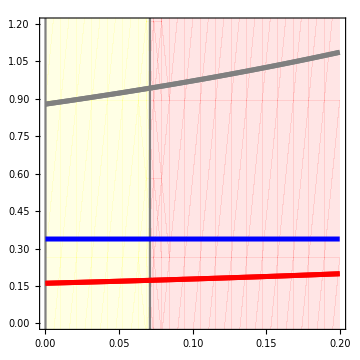

```mathematica
Show[
RegionPlot[0.071> x>-1,{x,0,0.2},{y,-1,11}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],
RegionPlot[0.5> x>0.071,{x,0,0.2},{y,-1,11}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],

Plot[Sstar,{theta,0.0,0.2}, PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Istar,{theta,0.0,0.2}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Istar,{theta,0.0,0.2}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Zstar*0.1,{theta,0.0,0.2}, PlotStyle->{Gray,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[Zstar*0.1,{theta,0.0,0.2}, PlotStyle->{Gray,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{All,{0,1.2}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

#### A5F

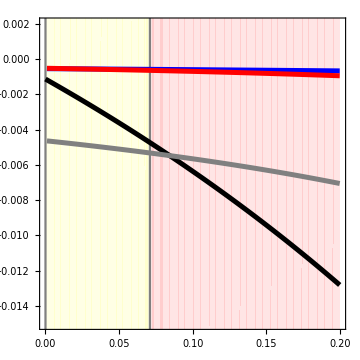

```mathematica
Show[
RegionPlot[0.071> x>-1,{x,0,0.2},{y,-1,11}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],
RegionPlot[0.5> x>0.071,{x,0,0.2},{y,-1,11}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],

Plot[(J11SIZ/.{S->Sstar,F->Istar,Z->Zstar}),{theta,0.0,0.2}, PlotStyle->{Black,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[direct/.{S->Sstar,F->Istar},{theta,0.001,0.2}, PlotStyle->{Blue,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[indirectI,{theta,0.001,0.2}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[indirectZ*0.1,{theta,0.001,0.2}, PlotStyle->{Gray,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{All,{-0.015,0.002}},
Frame->True,LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

### Loop Setup

```mathematica
Clear[e,h,f,dz,beta,v,o,theta,r,ds,k1]
```

#### Jacobian Elements

```mathematica
J11SIZ = FullSimplify[D[dSSIZ,S]];
J12SIZ = FullSimplify[D[dSSIZ,F]];
J13SIZ = FullSimplify[D[dSSIZ,Z]];
J21SIZ = FullSimplify[D[dFSIZ,S]];
J22SIZ = FullSimplify[D[dFSIZ,F]];
J23SIZ = FullSimplify[D[dFSIZ,Z]];
J31SIZ = FullSimplify[D[dZSIZ,S]];
J32SIZ = FullSimplify[D[dZSIZ,F]];
J33SIZ = FullSimplify[D[dZSIZ,Z]];
```

```mathematica
JMSIZ= {{J11SIZ,J12SIZ,J13SIZ},{J21SIZ,J22SIZ,J23SIZ},{J31SIZ,J32SIZ,J33SIZ}};
JMSIZ= JMSIZ//MatrixForm
```

(-ds-(f (F-k1+2 S+F theta+beta k1 Z))/k1 | -(f (S+(2 F-k1+S) theta))/k1 | -beta f S
beta f Z | -ds-v | beta f S
0 | o (ds+v) | -dz)

```mathematica
D[f*(S+theta*F)*(1-(S + F)/k1),S]
```

f (1-(F+S)/k1)-(f (S+F theta))/k1

```mathematica
DJac = {{jSS,jSF,jSZ},{jFS,jFF,jFZ},{0,jZF,jZZ}};
DJac//MatrixForm
```

```mathematica
CharacteristicPolynomial[DJac,x]
```

-jZF (jFZ jSS-jFS jSZ-jFZ x)+(jZZ-x) (-jFS jSF+jFF jSS-jFF x-jSS x+x^2)

```mathematica
Det[DJac]
```

-jFZ jSS jZF+jFS jSZ jZF-jFS jSF jZZ+jFF jSS jZZ

```mathematica
Tr[DJac]
```

jFF+jSS+jZZ

#### Feedbacks & Oscillation Criterion

```mathematica
SIZL1 = FullSimplify[(J11SIZ+J22SIZ+J33SIZ)];
SIZL2 = FullSimplify[(J12SIZ*J21SIZ-J11SIZ*J22SIZ)+(-J11SIZ*J33SIZ)+(J23SIZ*J32SIZ-J22SIZ*J33SIZ)];
SIZL3= -J23SIZ J11SIZ J32SIZ+J21SIZ J13SIZ J32SIZ-J21SIZ J12SIZ J33SIZ+J11SIZ J22SIZ J33SIZ;
OCSIZ = (SIZL1 SIZL2)+SIZL3;
```

### Loop Plots (F5)

```mathematica
Clear[k1,ds]
f = 0.1;
dz = 0.9;
beta= 0.055;
v = 0.05157;
o = 483.8;
theta = 0.06;
k1 = 30;
```

```mathematica
solsSIZ = Solve[{dSSIZ==0,dFSIZ==0,dZSIZ==0},{S,F,Z},WorkingPrecision->MachinePrecision];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
solsSIZ[[3]]/.{ds->0.05}
```

{S→0.338231,F→0.170768,Z→9.32386}

```mathematica
saddleSIZ = solsSIZ[[3]];
```

#### F5A (Upper v. Lower)

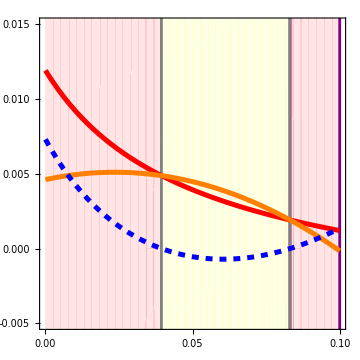

```mathematica
Show[
RegionPlot[0.0394> x>-1,{x,0,0.1},{y,-5,5}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[1> x>0.0831,{x,0,0.1},{y,-5,5}, BoundaryStyle->Purple,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0831> x>0.0394,{x,0,0.1},{y,-5,5}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[SIZL1 * SIZL2/.saddleSIZ,{ds,0,0.1}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[-SIZL3/.saddleSIZ,{ds,0,0.1}, PlotStyle->{Orange,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[OCSIZ/.saddleSIZ,{ds,0,0.1}, PlotStyle->{Blue,Dashed,Thickness[0.01]},AspectRatio->1,LabelStyle->16],


PlotRange->{All,{-0.005,0.015}},
Frame->True,
FrameTicks->{{{-0.005,{0.00, "0.000"},0.005,{0.01, "0.010"},0.015},None},{{{0.00, "0.00"},0.05,{0.10, "0.10"}},None}}, LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

#### F5B (F1 v. F2)

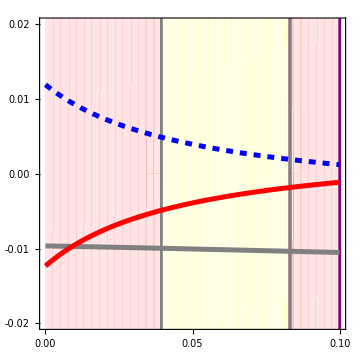

```mathematica
Show[
RegionPlot[0.0394> x>-1,{x,0,0.1},{y,-5,5}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[1> x>0.0831,{x,0,0.1},{y,-5,5}, BoundaryStyle->Purple,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0831> x>0.0394,{x,0,0.1},{y,-5,5}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[SIZL1 * SIZL2/.saddleSIZ,{ds,0,0.1}, PlotStyle->{Blue,Dashed,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

Plot[(SIZL1 /.saddleSIZ )*0.01,{ds,0,0.1}, PlotStyle->{Gray,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[SIZL2/.saddleSIZ,{ds,0,0.1}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{All,{-0.02,0.02}},
Frame->True,
FrameTicks->{{{-0.02,-0.01,{0.00, "0.00"},0.01,0.02},None},{{{0.00, "0.00"},0.05,{0.10, "0.10"}},None}},LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

#### F5C

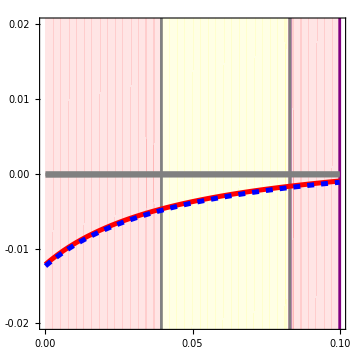

```mathematica
Show[
RegionPlot[0.0394> x>-1,{x,0,0.1},{y,-5,5}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[1> x>0.0831,{x,0,0.1},{y,-5,5}, BoundaryStyle->Purple,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0831> x>0.0394,{x,0,0.1},{y,-5,5}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[(J12SIZ*J21SIZ-J11SIZ*J22SIZ)/.saddleSIZ ,{ds,0,0.1}, PlotStyle->{Gray,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[(-J11SIZ*J33SIZ)/.saddleSIZ,{ds,0,0.1}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[(J23SIZ*J32SIZ-J22SIZ*J33SIZ) /.saddleSIZ,{ds,0,0.1}, PlotStyle->{Gray,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

Plot[SIZL2 /.saddleSIZ,{ds,0,0.1}, PlotStyle->{Blue,Dashed,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{All,{-0.02,0.02}},
Frame->True,
FrameTicks->{{{-0.02,-0.01,{0.00, "0.00"},0.01,0.02},None},{{{0.00, "0.00"},0.05,{0.10, "0.10"}},None}}, LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

#### F5D

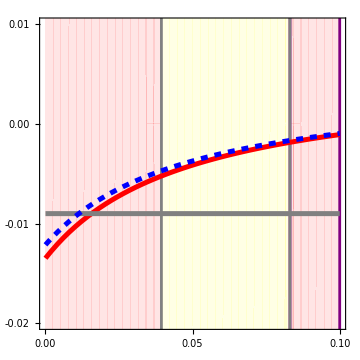

```mathematica
Show[
RegionPlot[0.0394> x>-1,{x,0,0.1},{y,-5,5}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[1> x>0.0831,{x,0,0.1},{y,-5,5}, BoundaryStyle->Purple,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0831> x>0.0394,{x,0,0.1},{y,-5,5}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[J11SIZ/.saddleSIZ ,{ds,0,0.1}, PlotStyle->{Red,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[(J33SIZ)*0.01/.saddleSIZ,{ds,0,0.1}, PlotStyle->{Gray,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

Plot[(-J11SIZ*J33SIZ) /.saddleSIZ,{ds,0,0.1}, PlotStyle->{Blue,Dashed,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{All,{-0.02,0.01}},
Frame->True,
FrameTicks->{{{-0.02,-0.01,{0.00, "0.00"},0.01,0.02},None},{{{0.00, "0.00"},0.05,{0.10, "0.10"}},None}},LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```

#### F5E

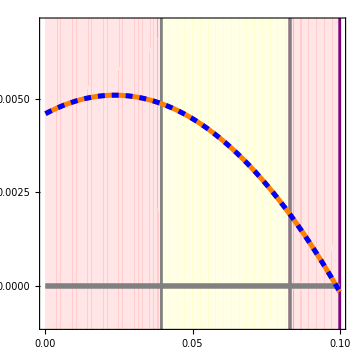

```mathematica
Show[
RegionPlot[0.0394> x>-1,{x,0,0.1},{y,-0.5,5}, BoundaryStyle->None,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[1> x>0.0831,{x,0,0.1},{y,-5,5}, BoundaryStyle->Purple,PlotStyle->{Red, Opacity[0.1]}],
RegionPlot[0.0831> x>0.0394,{x,0,0.1},{y,-5,5}, BoundaryStyle->Gray,PlotStyle->{Yellow, Opacity[0.1]}],

Plot[-J21SIZ (J32SIZ J13SIZ-J12SIZ J33SIZ)/.saddleSIZ,{ds,0,0.1}, PlotStyle->{Orange,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[-J31SIZ (J23SIZ J12SIZ-J13SIZ J22SIZ) /.saddleSIZ,{ds,0,0.1}, PlotStyle->{Gray,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[-J11SIZ (J22SIZ J33SIZ - J32SIZ J23SIZ)/.saddleSIZ ,{ds,0,0.1}, PlotStyle->{Gray,Thickness[0.01]},AspectRatio->1,LabelStyle->16],
Plot[-SIZL3 /.saddleSIZ,{ds,0,0.1}, PlotStyle->{Blue,Dashed,Thickness[0.01]},AspectRatio->1,LabelStyle->16],

PlotRange->{All,{-0.001,0.007}},
Frame->True,
FrameTicks->{{{-0.0025,{0.00, "0.0000"},0.0025,{0.005, "0.0050"}},None},{{{0.00, "0.00"},0.05,{0.10, "0.10"}},None}},LabelStyle->{Black,16},ImageSize->Medium, Axes->True
]
```